# R51 Triplet + C2H2 1st

## CTST

## Functions

### Document

ReadCTSTFile[filename]: read Thermo CTST output file; output format {string, 2-dim array} (we call it CTSTData format in the following)
CTSTUnit[CTSTData]: convert unit from (molecule/cc)^n to (mol/cc)^n
CTSTFit[CTSTData, Tempin]: fitting and output FITData format {formular, kinf(Tempin),relative error of fitting, kinfTemp array}: fit unit coverted kinf to 3 parameter form; output kinf(T=Tempin); relative error of fitting, {Temp,kinf} array for further plotting

CTSTFitDriver: ReadCTSTFile, CTSTUnit, and CTSTFit 3 in 1. output is the same as CTSTFit's output
CTSTOutput: Plotting

### Functions

```mathematica
ReadCTSTFile[Name_]:= Module[    (*Read Thermo CTST output file*)
{str,iline,iRead,str1,str2,unitString,str3,Data,strData,temp},
str = OpenRead[Name];
iline = 0; iRead = True;
(* Find Keyword "Species Properties"*)
While [ iRead == True,
str1 = Read[str,String]; iline = iline +1;
If [str1 == "Species Properties", (*Print[iline];*)iRead=False];
If [str1 == EndOfFile,Print["NO Keyword 'Species Properties' Found"];iRead=False]
];
iRead = True;
While[iRead == True,
str2 = Read[str,Word];
If[str2==EndOfFile,Print["NO Keyword 'Rate' Found"];iRead=False];
If[str2=="RATE",  (*find keyword "Rate"*)
unitString=Read[str,String]; (*find the unit of kinf*)
str3 = Read[str,String]; 
(*Read Data*)
Data={};
While[iRead== True,
strData = Read[str,String];
If[strData==EndOfFile,Break[]];
 temp=ReadList[StringToStream[strData],Number];
AppendTo[Data,temp];
];
iRead = False;(*Print["Reading "<>Name<>" Finished"];*)
];
];
Close[Name]; {unitString,Data}
];
CTSTUnit[Data_]:= Module[ (*convert unit from (molecule/cc)^n to (mol/cc)^n*)
{str,str1,unit,DataTemp},
DataTemp=Data⟦2⟧;
str=StringCases[Data⟦1⟧,RegularExpression["\\(..\\)"]];
str1=StringReplace[str,{"("-> "",")"-> ""}];
If [str1⟦1⟧==" 0",unit="1/s",If[str1⟦1⟧=="-1",unit="cc/mol/s",Print["Incorrect Unit"]]];
If[unit=="cc/mol/s",For[i=1,i<=Length[DataTemp],i++, DataTemp⟦i,2⟧=DataTemp⟦i,2⟧*6.02*10^23]];
{unit,DataTemp}
];
CTSTFit[Data_,TempIn_]:=Module[ (*Fit k=AT^nExp[-Ea/kT]*)
{Temp,kinf,kinfTemp,logfit,A1,n1,Ea1,AnE,relerror},
Temp=Data⟦2,All,1⟧;kinf=Data⟦2,All,2⟧;
kinfTemp=Data⟦2,All,1;;2⟧;
(*FindFit[kinfTemp,A*T^n*ⅇ^(-Ea/(1.987*10^-3*T)),{A,n,Ea},T]*)
(*{A1,n1,Ea1}=FindFit[kinfTemp,A*T^n*ⅇ^(-Ea/T),{{A,2.6608399999999996*^7},{n,0},{Ea,12718}},T]⟦All,2⟧;*)
AnE=NonlinearModelFit[kinfTemp,A*T^n*ⅇ^(-Ea/T),{A,n,Ea},T,MaxIterations-> 10000];
(*logfit=Fit[kinfTemp,{1,Log[T],1/T},T];
{logfit,FullSimplify[Exp[logfit]]}*)
(*Show[{ListPlot[kinfTemp],Plot[A1*T^n1*ⅇ^(-Ea1/T),{T,1000,2000}]}];*)
relerror=Table[0,{i,1,Length[Temp]}];
(*For[i=1,i≤Length[Temp],i++,relerror⟦i⟧ = (kinf⟦i⟧-A1*T^n1*ⅇ^(-Ea1/T)/.T-> Temp⟦i⟧)/kinf⟦i⟧];*)
For[i=1,i≤Length[Temp],i++,relerror⟦i⟧ = (kinf⟦i⟧-AnE[Temp⟦i⟧])/kinf⟦i⟧];
(*{{A1,n1,Ea1},A1*T^n1*ⅇ^(-Ea1/T)/.T-> TempIn,relerror,kinfTemp}*)
{Normal[AnE],{TempIn,AnE[TempIn]},relerror,kinfTemp,Data⟦1⟧}
];
CTSTFitDriver[Name_,TempIn_]:=Module[(* ReadCTSTFile,CTSTUnit and CTSTFit 3 in 1 *)
{ctstRawData,ctstData1,ctstfitData},
ctstRawData=ReadCTSTFile[Name];
ctstData1 = CTSTUnit[ctstRawData];
ctstfitData = CTSTFit[ctstData1,TempIn];
ctstfitData
];
CTSTOutput[FitData_]:=Module[ (*plot kinfTemp array and fitting curve; fitting error; and kinf(TempInterest)*)
{plotframedGT,plot1,plot2},
plotframedGT={{Style["k_∞("<>FitData⟦5⟧<>")",Italic,17],},{Style["Temperature (K)",Italic,17],}};
plot1 = ListLogPlot[FitData⟦4⟧,
                   Frame-> {{True,True},{True,True}},FrameLabel->plotframedGT,FrameTicksStyle->16,
                  AspectRatio-> 1/GoldenRatio,
                  AxesStyle->Dashed,
                  PlotMarkers-> {Automatic,Medium}
                    (*PlotLabel(*Legend*)->Style["DB5C triplet + benzene singlet → phenly-DB5C + H + H, Θ = 1 atm, torsion, 5C site","Title",Bold,15]*)];
plot2=LogPlot[FitData⟦1⟧,{T,1000,2000},
                   Frame-> {{True,True},{True,True}},FrameLabel->plotframedGT,FrameTicksStyle->16,
                  AspectRatio-> 1/GoldenRatio,
                  AxesStyle->Dashed
                    (*PlotLabel(*Legend*)->Style["DB5C triplet + benzene singlet → phenly-DB5C + H + H, Θ = 1 atm, torsion, 5C site","Title",Bold,15]*)];
Print["Fitting Formula: ",FitData⟦1⟧,"\nUnit: ",FitData⟦5⟧,"\nMax Fitting Error: ",Max[Abs[FitData⟦3⟧]],"\nk_∞(TempInterest)= ",FitData⟦2⟧];
Show[plot1,plot2]
]
```

### Debug

```mathematica
R1kffit=CTSTFitDriver["Reax1kf.out",1500]
```

{12448.6 ⅇ^(-10123.7/T) T^2.57569,{1500,2.21119×10^9},{-0.0011275,-0.000558399,-0.000539417,-0.000473448,-0.000440156,-0.0000189508,-0.0000439065,0.000270103,-0.000131906,7.61361×10^-6,4.30237×10^-6},{{1000.,2.66084×10^7},{1100.,8.54238×10^7},{1200.,2.30145×10^8},{1300.,5.41258×10^8},{1400.,1.1426×10^9},{1500.,2.21115×10^9},{1600.,3.98103×10^9},{1700.,6.75444×10^9},{1800.,1.08902×10^10},{1900.,1.68319×10^10},{2000.,2.50733×10^10}},cc/mol/s}

Fitting Formula: 12448.6 ⅇ^(-10123.7/T) T^2.57569
Unit: cc/mol/s
Max Fitting Error: 0.0011275
k_∞(TempInterest)= {1500,2.21119×10^9}

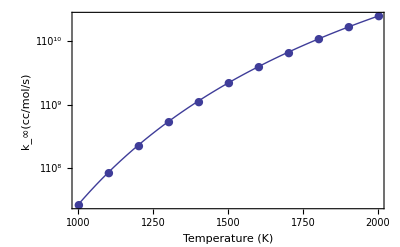

```mathematica
CTSTOutput[R1kffit]
```

## Gobal Setting

```mathematica
TempInterest=1500(*Temperature interested, kinf(T=TempInterest) will shown on PES*)
```

1500

```mathematica
cwd = NotebookDirectory[];
SetDirectory[NotebookDirectory[]]
```

C:\Users\dodo\Desktop\soothair_2nd\2_Systems_FullRev\R51_1st\Results\CTST

```mathematica
(*FileNames["*.out",cwd,2]*)
CTSTFileName=FileNames["*.out"]
```

{Reax1kb.out,Reax1kf.out,Reax2kb.out,Reax2kf.out,Reax3kb.out,Reax3kf.out}

## Reactions one by one

### Reax1 backward. IM1 -> TS1

```mathematica
R1kbFIT=CTSTFitDriver[CTSTFileName⟦1⟧,TempInterest]
```

{6.93285×10^13 ⅇ^(-7694.44/T) T^0.0976301,{1500,8.37963×10^11},{0.00696677,0.00249082,0.000808125,-0.000370163,-0.000513969,-0.000313843,0.0000214351,-0.000024037,0.000186005,0.0000221127,-0.0000544155},{{1000.,6.24×10^10},{1100.,1.262×10^11},{1200.,2.276×10^11},{1300.,3.752×10^11},{1400.,5.767×10^11},{1500.,8.377×10^11},{1600.,1.162×10^12},{1700.,1.551×10^12},{1800.,2.006×10^12},{1900.,2.525×10^12},{2000.,3.107×10^12}},1/s}

Fitting Formula: 6.93285×10^13 ⅇ^(-7694.44/T) T^0.0976301
Unit: 1/s
Max Fitting Error: 0.00696677
k_∞(TempInterest)= {1500,8.37963×10^11}

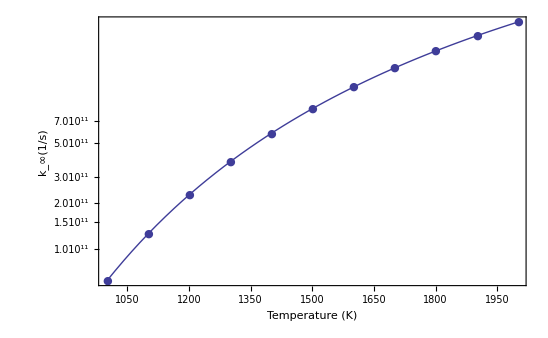

```mathematica
%//CTSTOutput
```

### Reax1 forward. R51tri + C2H2 -> TS1

```mathematica
R1kfFIT=CTSTFitDriver[CTSTFileName⟦2⟧,TempInterest]
```

{12448.6 ⅇ^(-10123.7/T) T^2.57569,{1500,2.21119×10^9},{-0.0011275,-0.000558399,-0.000539417,-0.000473448,-0.000440156,-0.0000189508,-0.0000439065,0.000270103,-0.000131906,7.61361×10^-6,4.30237×10^-6},{{1000.,2.66084×10^7},{1100.,8.54238×10^7},{1200.,2.30145×10^8},{1300.,5.41258×10^8},{1400.,1.1426×10^9},{1500.,2.21115×10^9},{1600.,3.98103×10^9},{1700.,6.75444×10^9},{1800.,1.08902×10^10},{1900.,1.68319×10^10},{2000.,2.50733×10^10}},cc/mol/s}

```mathematica
%//CTSTOutput
```

Fitting Formula: 12448.6 ⅇ^(-10123.7/T) T^2.57569
Unit: cc/mol/s
Max Fitting Error: 0.0011275
k_∞(TempInterest)= {1500,2.21119×10^9}

-Graphics-

### Reax2 backward. IM2 -> TS2

```mathematica
R2kbFIT=CTSTFitDriver[CTSTFileName⟦3⟧,TempInterest]
```

{1.33566×10^13 ⅇ^(-1871.01/T) T^0.0660533,{1500,6.21978×10^12},{0.000757723,-0.000156033,-0.000421147,-0.000284943,-0.000127367,0.000035781,0.000178998,0.000183082,0.000154654,0.0000153004,-0.000203459},{{1000.,3.248×10^12},{1100.,3.871×10^12},{1200.,4.485×10^12},{1300.,5.084×10^12},{1400.,5.663×10^12},{1500.,6.22×10^12},{1600.,6.754×10^12},{1700.,7.264×10^12},{1800.,7.751×10^12},{1900.,8.215×10^12},{2000.,8.657×10^12}},1/s}

Fitting Formula: 1.33566×10^13 ⅇ^(-1871.01/T) T^0.0660533
Unit: 1/s
Max Fitting Error: 0.000757723
k_∞(TempInterest)= {1500,6.21978×10^12}

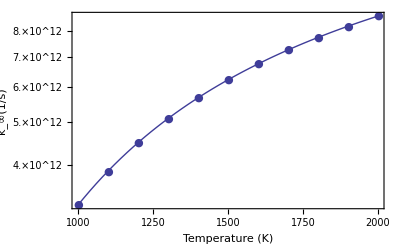

```mathematica
%//CTSTOutput
```

### Reax2 forward. IM1 -> TS2

```mathematica
R2kfFIT=CTSTFitDriver[CTSTFileName⟦4⟧,TempInterest]
```

{1.23142×10^13 ⅇ^(-1619.79/T) T^0.0788293,{1500,7.44384×10^12},{0.000778691,-0.000210834,-0.000464422,-0.000277306,-0.000129305,0.000021096,0.000225289,0.000230781,0.000144383,0.0000345418,-0.000248593},{{1000.,4.205×10^12},{1100.,4.904×10^12},{1200.,5.581×10^12},{1300.,6.232×10^12},{1400.,6.853×10^12},{1500.,7.444×10^12},{1600.,8.006×10^12},{1700.,8.538×10^12},{1800.,9.042×10^12},{1900.,9.52×10^12},{2000.,9.972×10^12}},1/s}

Fitting Formula: 1.23142×10^13 ⅇ^(-1619.79/T) T^0.0788293
Unit: 1/s
Max Fitting Error: 0.000778691
k_∞(TempInterest)= {1500,7.44384×10^12}

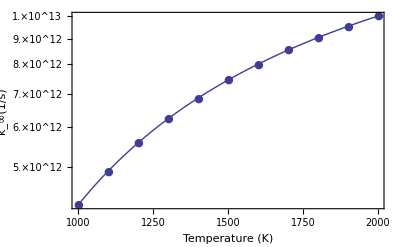

```mathematica
%//CTSTOutput
```

### Reax3 backward. P1 -> TS3

```mathematica
R3kbFIT=CTSTFitDriver[CTSTFileName⟦5⟧,TempInterest]
```

{2.65127×10^11 ⅇ^(-33397.5/T) T^0.528231,{1500,2701.4},{0.0667182,0.039066,0.0221047,0.011937,0.00603011,0.00280654,0.000943886,0.000288647,-0.000175936,0.000029539,-1.85592×10^-6},{{1000.,0.03418},{1100.,0.727},{1200.,9.391},{1300.,82.48},{1400.,534.2},{1500.,2709.},{1600.,11250.},{1700.,39630.},{1800.,121600.},{1900.,332300.},{2000.,822200.}},1/s}

Fitting Formula: 2.65127×10^11 ⅇ^(-33397.5/T) T^0.528231
Unit: 1/s
Max Fitting Error: 0.0667182
k_∞(TempInterest)= {1500,2701.4}

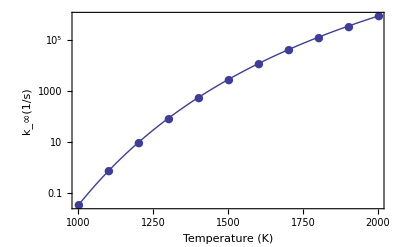

```mathematica
%//CTSTOutput
```

### Reax3 forward. IM2 -> TS3

```mathematica
R3kfFIT=CTSTFitDriver[CTSTFileName⟦6⟧,TempInterest]
```

{4.92872×10^10 ⅇ^(-13359.4/T) T^0.561572,{1500,4.05882×10^8},{0.0412573,0.0210009,0.0100939,0.00413488,0.00107945,0.0000454251,-0.000300421,-0.000472062,0.0000456437,0.000192284,-0.0000592493},{{1000.,3.925×10^6},{1100.,1.366×10^7},{1200.,3.903×10^7},{1300.,9.555×10^7},{1400.,2.069×10^8},{1500.,4.059×10^8},{1600.,7.341×10^8},{1700.,1.241×10^9},{1800.,1.984×10^9},{1900.,3.023×10^9},{2000.,4.421×10^9}},1/s}

Fitting Formula: 4.92872×10^10 ⅇ^(-13359.4/T) T^0.561572
Unit: 1/s
Max Fitting Error: 0.0412573
k_∞(TempInterest)= {1500,4.05882×10^8}

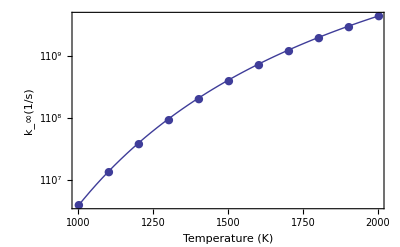

```mathematica
%//CTSTOutput
```

## All Reactions

Reax1kb.out

Fitting Formula: 6.93285×10^13 ⅇ^(-7694.44/T) T^0.0976301
Unit: 1/s
Max Fitting Error: 0.00696677
k_∞(TempInterest)= {1500,8.37963×10^11}

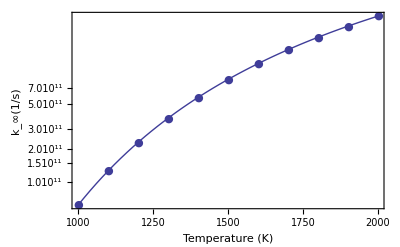

Reax1kf.out

Fitting Formula: 12448.6 ⅇ^(-10123.7/T) T^2.57569
Unit: cc/mol/s
Max Fitting Error: 0.0011275
k_∞(TempInterest)= {1500,2.21119×10^9}

-Graphics-

Reax2kb.out

Fitting Formula: 1.33566×10^13 ⅇ^(-1871.01/T) T^0.0660533
Unit: 1/s
Max Fitting Error: 0.000757723
k_∞(TempInterest)= {1500,6.21978×10^12}

-Graphics-

Reax2kf.out

Fitting Formula: 1.23142×10^13 ⅇ^(-1619.79/T) T^0.0788293
Unit: 1/s
Max Fitting Error: 0.000778691
k_∞(TempInterest)= {1500,7.44384×10^12}

-Graphics-

Reax3kb.out

Fitting Formula: 2.65127×10^11 ⅇ^(-33397.5/T) T^0.528231
Unit: 1/s
Max Fitting Error: 0.0667182
k_∞(TempInterest)= {1500,2701.4}

-Graphics-

Reax3kf.out

Fitting Formula: 4.92872×10^10 ⅇ^(-13359.4/T) T^0.561572
Unit: 1/s
Max Fitting Error: 0.0412573
k_∞(TempInterest)= {1500,4.05882×10^8}

-Graphics-

```mathematica
For[j=1,j≤Length[CTSTFileName],j++,
Print[CTSTFileName⟦j⟧];
(*Print[CTSTFitDriver[CTSTFileName⟦j⟧,TempInterest]];*)
CTSTFitDriver[CTSTFileName⟦j⟧,TempInterest]//CTSTOutput//Print
]
```

## Kinetic Analysis

R1+C2H2 -- IM1 -- IM2 -- P1

### Preparation

```mathematica
kinfTempIn=Table[0,{i,1,Length[CTSTFileName]}];
s="";
For[j=1,j≤ Length[CTSTFileName],j++,
kinfTempIn⟦j⟧=CTSTFitDriver[CTSTFileName⟦j⟧,TempInterest]⟦2,2⟧;
s=s<>CTSTFileName⟦j⟧<>": "<>ToBoxes[kinfTempIn⟦j⟧]<>"\n"
];
Print[s//ScientificForm];
Print[kinfTempIn]
```

Reax1kb.out: 8.379629065456139`*^11
Reax1kf.out: 2.2111879030775495`*^9
Reax2kb.out: 6.219777442012031`*^12
Reax2kf.out: 7.443842961699087`*^12
Reax3kb.out: 2701.397095677703`
Reax3kf.out: 4.058815619579826`*^8

{8.37963×10^11,2.21119×10^9,6.21978×10^12,7.44384×10^12,2701.4,4.05882×10^8}

```mathematica
kinfTempIn⟦2⟧/kinfTempIn⟦1⟧*kinfTempIn⟦6⟧
```

1.07103×10^6

```mathematica
kinfTempIn⟦2⟧/kinfTempIn⟦1⟧*kinfTempIn⟦4⟧/kinfTempIn⟦3⟧*kinfTempIn⟦6⟧
```

1.28181×10^6

### Kinetic System

k_(1f) : R1 -> IM1
k_(1b) : IM1 -> R1
k_(2f) : IM1 -> IM2
k_(2b) : IM2 -> IM1
k_(3f) : IM2 -> P1
k_(3b) : P1 -> IM2

#### equations

```mathematica
R1Increase=k1b*IM1[t]-k1f*R1[t]*C2H2
IM1Increase=k1f*R1[t]*C2H2+k2b*IM2[t]-(k1b+k2f)*IM1[t]
IM2Increase=k2f*IM1[t]+k3b*P1[t]-(k2b+k3f)*IM2[t]
P1Increase=k3f*IM2[t]-k3b*P1[t]
```

k1b IM1[t]-C2H2 k1f R1[t]

-(k1b+k2f) IM1[t]+k2b IM2[t]+C2H2 k1f R1[t]

k2f IM1[t]-(k2b+k3f) IM2[t]+k3b P1[t]

k3f IM2[t]-k3b P1[t]

#### quasi static steady approximation applied to IM1 and IM2

```mathematica
IM1IM2solution=Simplify[Solve[{IM1Increase==0,IM2Increase==0},{IM1[t],IM2[t]}]]
```

{{IM1[t]→(k2b k3b P1[t]+C2H2 k1f (k2b+k3f) R1[t])/(k2f k3f+k1b (k2b+k3f)),IM2[t]→((k1b+k2f) k3b P1[t]+C2H2 k1f k2f R1[t])/(k2f k3f+k1b (k2b+k3f))}}

```mathematica
{{R1IncreaseQSS,P1IncreaseQSS}}=Simplify[{R1Increase,P1Increase}/.IM1IM2solution]
```

{{(k1b k2b k3b P1[t]-C2H2 k1f k2f k3f R1[t])/(k2f k3f+k1b (k2b+k3f)),(-k1b k2b k3b P1[t]+C2H2 k1f k2f k3f R1[t])/(k2f k3f+k1b (k2b+k3f))}}

```mathematica
FullSimplify[DSolve[{R1'[t]==R1IncreaseQSS,P1'[t]==P1IncreaseQSS,P1[0]==0},{R1,P1},t]]
```

{{R1→Function[{t},((k1b k2b k3b+C2H2 ⅇ^(((-k1b k2b k3b-C2H2 k1f k2f k3f) t)/(k1b k2b+k1b k3f+k2f k3f)) k1f k2f k3f) C[1])/(k1b k2b k3b+C2H2 k1f k2f k3f)],P1→Function[{t},-(C2H2 (-1+ⅇ^(((-k1b k2b k3b-C2H2 k1f k2f k3f) t)/(k1b k2b+k1b k3f+k2f k3f))) k1f k2f k3f C[1])/(k1b k2b k3b+C2H2 k1f k2f k3f)]}}

```mathematica
R1P1Solutions=FullSimplify[DSolve[{R1'[t]==R1IncreaseQSS,P1'[t]==P1IncreaseQSS,R1[0]==R1ini,P1[0]==0},{R1,P1},t]]⟦1⟧
```

{R1→Function[{t},((k1b k2b k3b+C2H2 ⅇ^(((-k1b k2b k3b-C2H2 k1f k2f k3f) t)/(k1b k2b+k1b k3f+k2f k3f)) k1f k2f k3f) R1ini)/(k1b k2b k3b+C2H2 k1f k2f k3f)],P1→Function[{t},-(C2H2 (-1+ⅇ^(((-k1b k2b k3b-C2H2 k1f k2f k3f) t)/(k1b k2b+k1b k3f+k2f k3f))) k1f k2f k3f R1ini)/(k1b k2b k3b+C2H2 k1f k2f k3f)]}

#### equilibrium concentration from species profile

equilibrium concentration of R1:

```mathematica
(*Limit[R1P1Solutions⟦1,2,2⟧,t-> Infinity]*)
R1ini(k1b k2b k3b)/(k1b k2b k3b+C2H2 k1f k2f k3f)
```

(k1b k2b k3b R1ini)/(k1b k2b k3b+C2H2 k1f k2f k3f)

equilibrium concentration of P1:

```mathematica
R1ini(C2H2  k1f k2f k3f)/(k1b k2b k3b+C2H2 k1f k2f k3f)
```

(C2H2 k1f k2f k3f R1ini)/(k1b k2b k3b+C2H2 k1f k2f k3f)

The overall equilibrium constant (P1eq/R1eq)

```mathematica
Keq=R1ini(C2H2  k1f k2f k3f)/(k1b k2b k3b+C2H2 k1f k2f k3f)/(R1ini(k1b k2b k3b)/(k1b k2b k3b+C2H2 k1f k2f k3f))
```

(C2H2 k1f k2f k3f)/(k1b k2b k3b)

```mathematica
Keq/.{k1f-> kinfTempIn⟦2⟧,k2f-> kinfTempIn⟦4⟧,k3f-> kinfTempIn⟦6⟧,k1b-> kinfTempIn⟦1⟧,k2b-> kinfTempIn⟦3⟧,k3b-> kinfTempIn⟦5⟧}
```

474.498 C2H2

where C2H2 in mol/cc. This means 47449.8*C2H2% of R1 is converted into P1. Assuming 2% mole fraction of C2H2, the converting fraction is

```mathematica
Keq/.{k1f-> kinfTempIn⟦2⟧,k2f-> kinfTempIn⟦4⟧,k3f-> kinfTempIn⟦6⟧,k1b-> kinfTempIn⟦1⟧,k2b-> kinfTempIn⟦3⟧,k3b-> kinfTempIn⟦5⟧,C2H2->0.02* 1/1500/82.0574587}
```

0.0000771001

around 7.7*10^-5 mole fraction of R1 converts into P1.

#### Forward kinf: assuming irreverisible of Reax 3

Solution of R1 with k3b=0

```mathematica
R1irrev=Simplify[R1P1Solutions⟦1,2,2⟧/.k3b-> 0]
```

ⅇ^(-(C2H2 k1f k2f k3f t)/(k2f k3f+k1b (k2b+k3f))) R1ini

```mathematica
kinffor=-D[Simplify[Log[R1irrev]],t](*unit 1/s, therefore kinffor is quasi unimolecular rate*)
```

(C2H2 k1f k2f k3f)/(k2f k3f+k1b (k2b+k3f))

```mathematica
kinffor/.{k1f-> kinfTempIn⟦2⟧,k2f-> kinfTempIn⟦4⟧,k3f-> kinfTempIn⟦6⟧,k1b-> kinfTempIn⟦1⟧,k2b-> kinfTempIn⟦3⟧}
```

1.28098×10^6 C2H2

Therefore bimolecular rate is 1.28*10^6 cc/mol/s

#### Forward kinf: approximations

Since k3f << k2b, and k2f*k3f << k1b*k2b, we can remove the unimportant terms in the denominator:

(C2H2 k1f k2f k3f)/(k2f k3f+k1b (k2b+k3f))~(C2H2 k1f k2f k3f)/(k1b k2b)=C2H2*K1eq*K2eq*k3f
Using the above approximated formula, the kinffor = 1.28181×10^6C2H2,deviated from its exact value 1.28098×10^6 C2H2 by 1 in thousand.

#### Backward kinf: assuming irreversible of Reax 1

Solution of P1 with k1f = 0, and with initial condition P1[t=0]=P1ini, R1[t=0]=0

```mathematica
R1P1SolutionsRevers=FullSimplify[DSolve[{R1'[t]==R1IncreaseQSS,P1'[t]==P1IncreaseQSS,R1[0]==0,P1[0]==P1ini},{R1,P1},t]]⟦1⟧
```

{R1→Function[{t},-((-1+ⅇ^(((-k1b k2b k3b-C2H2 k1f k2f k3f) t)/(k1b k2b+k1b k3f+k2f k3f))) k1b k2b k3b P1ini)/(k1b k2b k3b+C2H2 k1f k2f k3f)],P1→Function[{t},((ⅇ^(((-k1b k2b k3b-C2H2 k1f k2f k3f) t)/(k1b k2b+k1b k3f+k2f k3f)) k1b k2b k3b+C2H2 k1f k2f k3f) P1ini)/(k1b k2b k3b+C2H2 k1f k2f k3f)]}

```mathematica
R1rev=Simplify[R1P1SolutionsRevers⟦2,2,2⟧/.k1f-> 0]
```

ⅇ^(-(k1b k2b k3b t)/(k2f k3f+k1b (k2b+k3f))) P1ini

```mathematica
kinfbac=-D[Log[R1rev],t]
```

(k1b k2b k3b)/(k2f k3f+k1b (k2b+k3f))

```mathematica
kinfbac/.{k1f-> kinfTempIn⟦2⟧,k2f-> kinfTempIn⟦4⟧,k3f-> kinfTempIn⟦6⟧,k1b-> kinfTempIn⟦1⟧,k2b-> kinfTempIn⟦3⟧,k3b-> kinfTempIn⟦5⟧,C2H2->0.02* 1/1500/82.0574587}
```

2699.66

Therefore the overall backward rate constant is 2699.66 1/s

#### Backward kinf: approximations

Since k3f << k2b, and k2f*k3f << k1b*k2b, we can remove the unimportant terms in the denominator:

(k1b k2b k3b)/(k2f k3f+k1b (k2b+k3f))~(k1b k2b k3b)/(k2f k3f+k1b (k2b+k3f))=k3b
Using above approximation, the kinfbac=2701.397, deviated from its exact value 2699.66 by 1 in thousand

#### equilibrium constant from overall kf and kb

```mathematica
kinffor/kinfbac
```

(C2H2 k1f k2f k3f)/(k1b k2b k3b)

## Summary

### k_∞ for each reaction

```mathematica
For[j=1,j≤Length[CTSTFileName],j++,
Print[CTSTFileName⟦j⟧];
(*Print[CTSTFitDriver[CTSTFileName⟦j⟧,TempInterest]];*)
CTSTFitDriver[CTSTFileName⟦j⟧,TempInterest]//CTSTOutput//Print
]
```

Reax1kb.out

Fitting Formula: 6.93285×10^13 ⅇ^(-7694.44/T) T^0.0976301
Unit: 1/s
Max Fitting Error: 0.00696677
k_∞(TempInterest)= {1500,8.37963×10^11}

-Graphics-

Reax1kf.out

Fitting Formula: 12448.6 ⅇ^(-10123.7/T) T^2.57569
Unit: cc/mol/s
Max Fitting Error: 0.0011275
k_∞(TempInterest)= {1500,2.21119×10^9}

-Graphics-

Reax2kb.out

Fitting Formula: 1.33566×10^13 ⅇ^(-1871.01/T) T^0.0660533
Unit: 1/s
Max Fitting Error: 0.000757723
k_∞(TempInterest)= {1500,6.21978×10^12}

-Graphics-

Reax2kf.out

Fitting Formula: 1.23142×10^13 ⅇ^(-1619.79/T) T^0.0788293
Unit: 1/s
Max Fitting Error: 0.000778691
k_∞(TempInterest)= {1500,7.44384×10^12}

-Graphics-

Reax3kb.out

Fitting Formula: 2.65127×10^11 ⅇ^(-33397.5/T) T^0.528231
Unit: 1/s
Max Fitting Error: 0.0667182
k_∞(TempInterest)= {1500,2701.4}

-Graphics-

Reax3kf.out

Fitting Formula: 4.92872×10^10 ⅇ^(-13359.4/T) T^0.561572
Unit: 1/s
Max Fitting Error: 0.0412573
k_∞(TempInterest)= {1500,4.05882×10^8}

-Graphics-

### Species Profile (reverisble, and QSS for IM1 and IM2)

```mathematica
R1P1Solutions
```

{R1→Function[{t},((k1b k2b k3b+C2H2 ⅇ^(((-k1b k2b k3b-C2H2 k1f k2f k3f) t)/(k1b k2b+k1b k3f+k2f k3f)) k1f k2f k3f) R1ini)/(k1b k2b k3b+C2H2 k1f k2f k3f)],P1→Function[{t},-(C2H2 (-1+ⅇ^(((-k1b k2b k3b-C2H2 k1f k2f k3f) t)/(k1b k2b+k1b k3f+k2f k3f))) k1f k2f k3f R1ini)/(k1b k2b k3b+C2H2 k1f k2f k3f)]}

### The overall forward and backward rate constant

```mathematica
kinffor
```

(C2H2 k1f k2f k3f)/(k2f k3f+k1b (k2b+k3f))

```mathematica
kinfbac
```

(k1b k2b k3b)/(k2f k3f+k1b (k2b+k3f))

### aprroximated overall rate constant (k3f is smaller than k1b and k2b)

kinffor=(C2H2 k1f k2f k3f)/(k1b k2b)=C2H2*K1eq*K2eq*k3f
kinfbac=k3b

### At temperature interested

```mathematica
s="";
For[j=1,j≤ Length[CTSTFileName],j++,
s=s<>CTSTFileName⟦j⟧<>": "<>ToBoxes[kinfTempIn⟦j⟧]<>"\n"
];
Print[s//ScientificForm];
```

Reax1kb.out: 8.379629065456139`*^11
Reax1kf.out: 2.2111879030775495`*^9
Reax2kb.out: 6.219777442012031`*^12
Reax2kf.out: 7.443842961699087`*^12
Reax3kb.out: 2701.397095677703`
Reax3kf.out: 4.058815619579826`*^8

```mathematica
kinffor/.{k1f-> kinfTempIn⟦2⟧,k2f-> kinfTempIn⟦4⟧,k3f-> kinfTempIn⟦6⟧,k1b-> kinfTempIn⟦1⟧,k2b-> kinfTempIn⟦3⟧,k3b-> kinfTempIn⟦5⟧(*,C2H2->0.02* 1/1500/82.0574587*)}
```

1.28098×10^6 C2H2

```mathematica
kinfbac/.{k1f-> kinfTempIn⟦2⟧,k2f-> kinfTempIn⟦4⟧,k3f-> kinfTempIn⟦6⟧,k1b-> kinfTempIn⟦1⟧,k2b-> kinfTempIn⟦3⟧,k3b-> kinfTempIn⟦5⟧(*,C2H2->0.02* 1/1500/82.0574587*)}
```

2699.66

### substitution

```mathematica
substit={};
For[j=1,j≤Length[CTSTFileName],j++,
AppendTo[substit,{StringReplace[CTSTFileName⟦j⟧,{"Reax"-> "",".out"-> ""}]<>"→",CTSTFitDriver[CTSTFileName⟦j⟧,TempInterest]⟦1⟧}]
];
```

```mathematica
substit
```

{{1kb→,6.12729×10^12 ⅇ^(-5792.53/T) T^0.330501},{1kf→,603.955 ⅇ^(-20989.2/T) T^2.80844},{2kb→,1.30972×10^13 ⅇ^(-1796.35/T) T^0.0640805},{2kf→,1.53771×10^13 ⅇ^(-1386.74/T) T^0.0869504},{3kb→,8.40167×10^11 ⅇ^(-44455.3/T) T^0.74846},{3kf→,9.6736×10^10 ⅇ^(-15146.4/T) T^0.587545}}